```mathematica
S1={
{1,2,3},
{1->2,2->3 },
Green
}
S2={
{1,2,3},
{3->1 },
Blue
}
S={S1,S2}
```

{{1,2,3},{1->2,2->3},RGBColor[0, 1, 0]}

{{1,2,3},{3->1},RGBColor[0, 0, 1]}

{{{1,2,3},{1->2,2->3},RGBColor[0, 1, 0]},{{1,2,3},{3->1},RGBColor[0, 0, 1]}}

```mathematica
ShowMultiGraph[S_]:=Module[
{vertices, edges},
vertices = S[[1]][[1]];
styleSet[s_] := (Style[#,s[[3]]])&/@s[[2]];
edges = Catenate[ styleSet/@S];
Return[Graph[vertices, edges]];
];
```

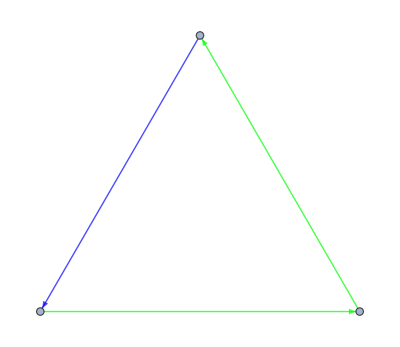

```mathematica
ShowMultiGraph[S]
```